```mathematica
Clear["Global`*"]
```

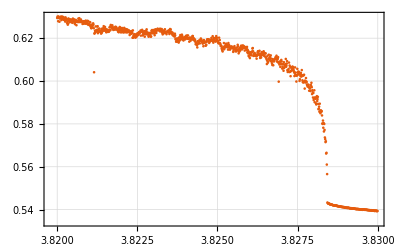

```mathematica
lista={};
n=20;
imax = 10^3;
For[j=3.820,j<3.83,j=j+10^-5,
μ=j;
sum=0;
For[k=1,k≤ n,k=k+1,
x=0.4+k/200;
For[i=1,i≤  400,i++,x = μ  x (1-x)];
For[i=1,i≤  imax,i++,
x = μ  x (1-x);
sum=sum+x;
];
];
media=sum/(n imax);
AppendTo[lista,{μ,media}]
]
ListPlot[lista,Frame->True,GridLines->Automatic]
```

```mathematica
RandomReal
```

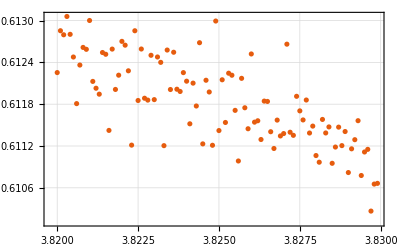

```mathematica
lista2={};
n=10^5;
imax = 3;
For[j=3.820,j<3.83,j=j+10^-4,
μ=j;
sum=0;
For[k=1,k≤ n,k=k+1,
x=RandomReal[{0,1}];(*0.4+k/200;*)
(*For[i=1,i≤  400,i++,x = μ  x (1-x)];*)
For[i=1,i≤  imax,i++,
x = μ  x (1-x);
sum=sum+x;
];
];
media=sum/(n imax);
AppendTo[lista2,{μ,media}]
]
ListPlot[lista2,Frame->True,GridLines->Automatic]
```

```mathematica
ListPlot[lista,GridLines->Automatic]
```

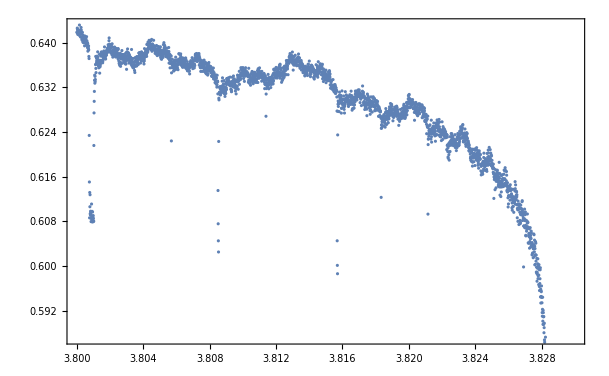
```mathematica
lis3=-Graphics-
```

-Graphics-

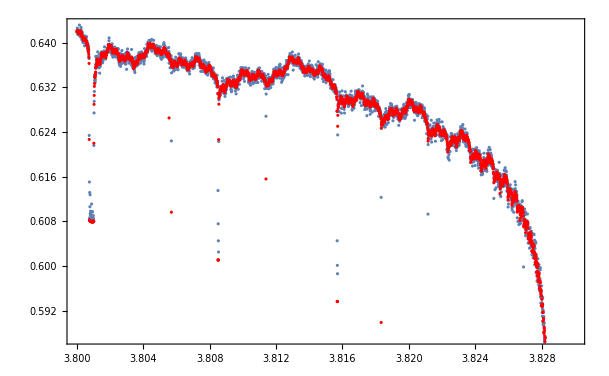

```mathematica
Show[lis3,ListPlot[lista,Frame->True,PlotStyle->Red]]
```

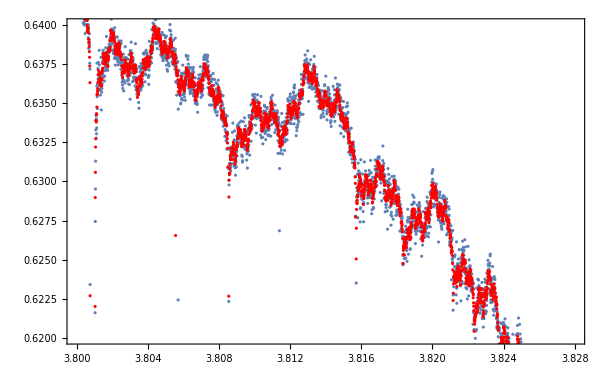

```mathematica
Show[lis3,ListPlot[lista,Frame->True,PlotStyle->Red],PlotRange-> {{3.8,3.828},{0.62,0.64}}]
```

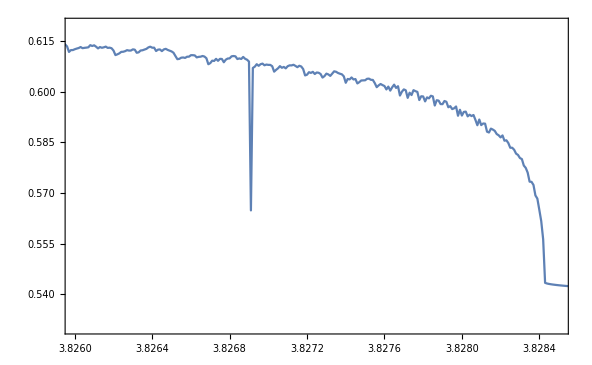

```mathematica
ListPlot[lista,Frame->True,Joined->True,PlotRange->{{3.826,3.8285},{0.53,0.62}}]
```

```mathematica
NotebookSave[EvaluationNotebook[]];
```

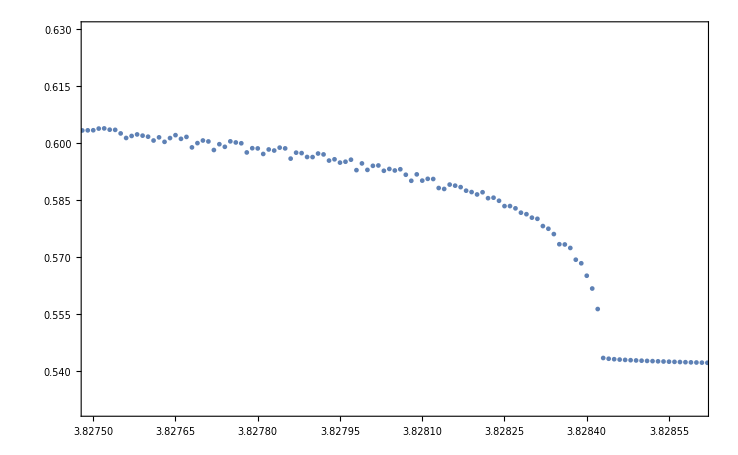

```mathematica
ListPlot[lista,Frame->True,Joined->False,PlotRange->{{3.8275,3.8286},{0.53,0.63}}]
```

```mathematica
ListPlot[lista,Frame->True,Joined->True,PlotRange->{{3.800,3.8285},Automatic}]
```